```mathematica
hm=ColorNegate@Binarize@ImageResize[Import[NotebookDirectory[]<>"hammer.jpg"],{500,500}];
```

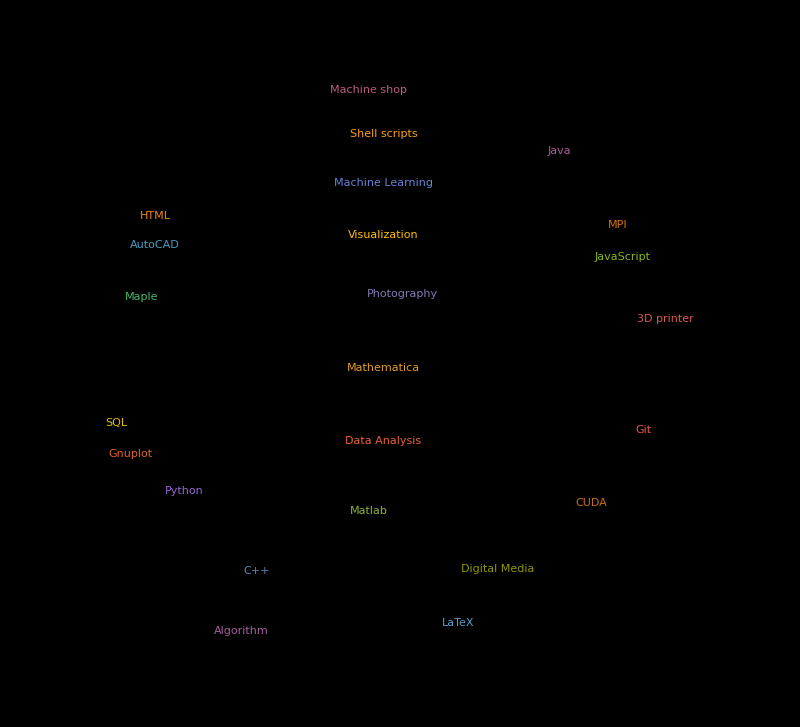

```mathematica
skills=({{Style["C++",Italic], 10}, {Style["Mathematica",Italic], 10}, {Style["Matlab",Italic], 9}, {"Shell scripts", 6}, {"JavaScript", 4}, {"Gnuplot", 3}, {"Python", 5}, {"Maple", 5}, {"CUDA", 7}, {"LaTeX", 7}, {"SQL", 5}, {"Git", 6}, {"Photography", 8}, {"AutoCAD", 4}, {"3D printer", 4}, {"Machine shop", 5}, {"Data Analysis", 8}, {"Machine Learning", 6}, {"Java", 4}, {"HTML", 4}, {"Digital Media", 6}, {"Algorithm", 6}, {"MPI", 5}, {"Visualization", 7}});
WordCloud[skills,WordSpacings->3,ImageSize->800]
```